```mathematica
SetDirectory["C:\\anaconda32\\Work\\OnlineModel\\SimulationFramework\\Examples\\FEBE_best_longitudinal"]
```

C:\anaconda32\Work\OnlineModel\SimulationFramework\Examples\FEBE_best_longitudinal

```mathematica
SetDirectory["\\\\apclara1\\jkj62\\OnlineModel\\SimulationFramework\\Examples\\test"]
```

\\apclara1\jkj62\OnlineModel\SimulationFramework\Examples\test

```mathematica
Import["./CLA-S07-DIA-BPM-03.hdf5","/Parameters/"]
```

Import::nffil: File not found during Import.

$Failed

```mathematica
Import["./CLA-S07-DIA-BPM-03.hdf5","/beam/columns"]
```

Import::nffil: File not found during Import.

$Failed

```mathematica
{x,y,z,cpx,cpy,cpz,t,q}=Transpose[Import["./CLA-S07-DIA-BPM-03.hdf5","/beam/beam"]];
```

Import::nffil: File not found during Import.

Set::shape: Lists {x,y,z,cpx,cpy,cpz,t,q} and Transpose[$Failed] are not the same shape.

```mathematica
lplot=ListPlot[{10^6 Transpose[{x,y}]},AspectRatio->Automatic,Frame->True,ImageSize->600,PlotStyle->{{Red,Opacity[0.1]}}]
```

-Graphics-

```mathematica
UnitConvert[Quantity[297,"Pounds Sterling"]/Quantity[10,"TB"],"p per GB"]//N
```

0.0297 £

```mathematica
UnitConvert[Quantity[378,"Pounds Sterling"]/Quantity[12,"TB"],"p per GB"]//N
```

0.0315 £

```mathematica
z[[1]]
```

41.3078

```mathematica
Transpose[{z,cpz}][[2]]
```

{41.3078,2.48522×10^8}

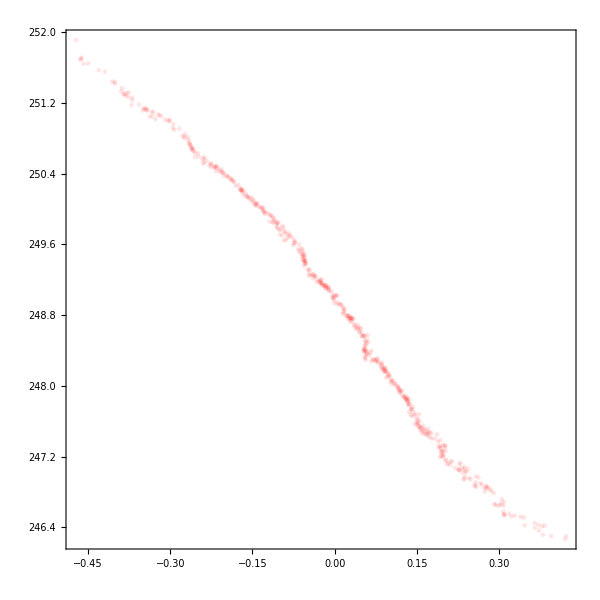

```mathematica
lplot=ListPlot[{Transpose[{10^12(z-Mean[z])/(2.99 10^8),10^-6 cpz}]},AspectRatio->1,Frame->True,ImageSize->600,PlotStyle->{{Red,Opacity[0.1]}}]
```

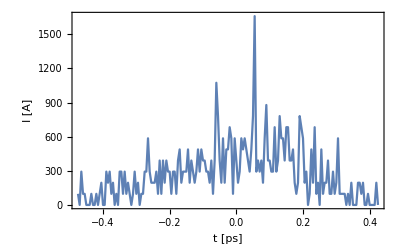

```mathematica
slicelength=0.005;
ListLinePlot[{#[[1]],Append[#[[2]],0]}//Transpose,Frame->True,PlotRange->{All,All},FrameLabel->{"t [ps]","I [A]"}]&[{1,250/(slicelength Length[#])}HistogramList[#,{slicelength}]]&[10^12(z-Mean[z])/(2.99 10^8)]
```

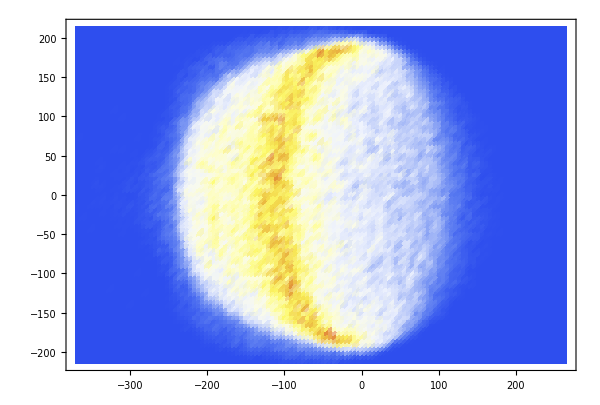

```mathematica
dplot=Block[{bins,hdata},
{bins,hdata}=HistogramList[10^6 Transpose[{x,y}],{100,100}];
ListDensityPlot[Transpose[hdata],AspectRatio->Automatic,ImageSize->600,DataRange->({#[[1]],#[[-1]]}&/@bins),Mesh->None,ColorFunction->(ColorData["TemperatureMap"])]]
```

## Plotting Emit Files with Elegant

```mathematica
bestsolutions1kA={{29713903.749112953,-29.21603152107705,25962771.986255325,-8.516380020664478,19361775.168006733,224.23790622197075,34612668.69890043,58.99106676994291,0.13286721490054315},{29713903.744701855,-29.216031521077053,25962772.29554525,-8.51638002066448,19361775.168006733,224.236826395808,34612668.69890043,58.99106676994291,0.13286721490054315},{29713903.56917426,-29.21603152107705,25962771.723306194,-8.51638002066448,19361775.168006733,224.23753315378553,34612668.69890043,58.991066769942904,0.13286721490054315},{29713903.386091314,-29.216031521077056,25962771.775294825,-8.516380020664476,19361775.168006733,224.23992083625888,34612668.69890043,58.991066769942904,0.13286721490054315},{29713903.645631373,-29.21603152107705,25962771.990313392,-8.516380020664482,19361775.168006733,224.252131099212,34612668.69890043,58.991066769942904,0.13286721490054315},{29713903.7445023,-29.21603152107705,25962772.95334911,-8.516380020664483,19361775.168006733,224.25310453008555,34612668.69890043,58.991066769942904,0.13286721490054315},{29713903.7445023,-29.216031521077053,25962772.95334911,-8.516380020664482,19361775.168006733,224.25310453008552,34612668.69890043,58.991066769942904,0.13286721490054315},{29713903.7445023,-29.21603152107705,25962772.95334911,-8.516380020664482,19361775.168006733,224.25310453008552,34612668.69890043,58.991066769942904,0.13286721490054315},{29713903.64536666,-29.216031521077053,25962773.008718535,-8.51638002066448,19361775.168006733,224.25314013196206,34612668.69890043,58.991066769942904,0.13286721490054315},{29713903.748913396,-29.21603152107705,25962772.64405918,-8.51638002066448,19361775.168006733,224.25418435624826,34612668.69890043,58.9910667699429,0.13286721490054315}};
```

```mathematica
<<astrainterpret`
```

```mathematica
<<sddsBinaryinterpret`
```

```mathematica
SetDirectory["\\\\apclara1\\jkj62\\OnlineModel\\SimulationFramework\\Examples\\CLARA\\CLARA_best_longitudinal"]
```

\\apclara1\jkj62\OnlineModel\SimulationFramework\Examples\CLARA\CLARA_best_longitudinal

```mathematica
ASTRAemitInterpret["./"~~#~~".Zemit.001"&/@{"L02","S03","L03","S04","L4H","S05","S06","L04","S07"},ASTRAVerbose->True]
```

Columns Redefined: z [m], t [ns], xavr [mm], xrms [mm], xprms [mrad], ϵxnorm [mm mrad π], xxpavr [mm mrad]

Columns Redefined: z [m], t [ns], yavr [mm], yrms [mm], yprms [mrad], ϵynorm [mm mrad π], yypavr [mm mrad]

Columns Redefined: z [m], t [ns], Ekin [MeV], zrms [mm], ΔErms [keV], ϵznorm [keV mm π], zEavr [keV]

```mathematica
sddsBinaryInterpret["./FMS.twi",sddsVerbose->True]
```

Number of Pages: 1

Variables (Re)Assigned: {s, betax, alphax, psix, etax, etaxp, xAperture, betay, alphay, psiy, etay, etayp, yAperture, pCentral0, ElementName, ElementOccurence, ElementType, dI1, dI2, dI3, dI4, dI5}

Parameters (Re)Assigned: {Step, nux, dnuxdp, dnuxdp2, dnuxdp3, Ax, AxLocation, nuy, dnuydp, dnuydp2, dnuydp3, Ay, AyLocation, deltaHalfRange, nuxChromUpper, nuxChromLower, nuyChromUpper, nuyChromLower, Stage, pCentral, dbetaxdp, dbetaydp, dalphaxdp, dalphaydp, etax2, etay2, etax3, etay3, etaxp2, etayp2, etaxp3, etayp3, betaxMin, betaxAve, betaxMax, betayMin, betayAve, betayMax, etaxMax, etayMax, waistsx, waistsy, dnuxdAx, dnuxdAy, dnuydAx, dnuydAy, dnuxdAx2, dnuxdAy2, dnuxdAxAy, dnuydAx2, dnuydAy2, dnuydAxAy, nuxTswaLower, nuxTswaUpper, nuyTswaLower, nuyTswaUpper, couplingIntegral, couplingDelta, emittanceRatio, alphac2, alphac, I1, I2, I3, I4, I5, ex0, enx0, taux, Jx, tauy, Jy, Sdelta0, taudelta, Jdelta, U0}

```mathematica
{betax,alphax,betay,alphay}[[All,1]]
```

{3.46214,1.60421,2.6919,-1.26558}

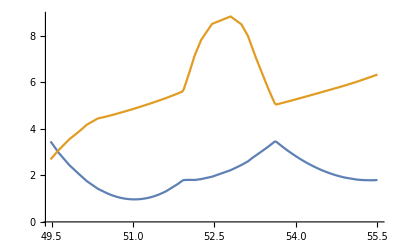

```mathematica
ListLinePlot[{Join[Transpose[{s+Last[z],betax}]],Join[Transpose[{s+Last[z],betay}]]},PlotRange->{All,All}]
```

```mathematica
sddsBinaryInterpret["./FMS.sig",sddsVerbose->True]
```

Number of Pages: 1

Variables (Re)Assigned: {s, ElementName, ElementOccurence, ElementType, s1, s12, s13, s14, s15, s16, s17, s2, s23, s24, s25, s26, s27, s3, s34, s35, s36, s37, s4, s45, s46, s47, s5, s56, s57, s6, s67, s7, ma1, ma2, ma3, ma4, ma5, ma6, ma7, minimum1, minimum2, minimum3, minimum4, minimum5, minimum6, minimum7, maximum1, maximum2, maximum3, maximum4, maximum5, maximum6, maximum7, Sx, Sxp, Sy, Syp, Ss, Sdelta, St, ex, enx, ecx, ecnx, ey, eny, ecy, ecny, betaxBeam, alphaxBeam, betayBeam, alphayBeam}

Parameters (Re)Assigned: {Step}

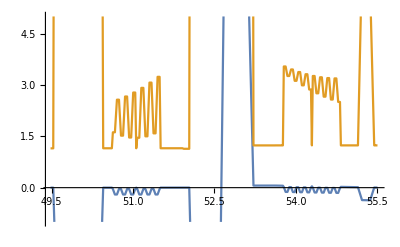

```mathematica
ListLinePlot[{Join[Transpose[{s+Last[z],10^3 etax}]],Join[Transpose[{s+Last[z],10^6 enx}]]},PlotRange->{All,{-1,5}}]
```

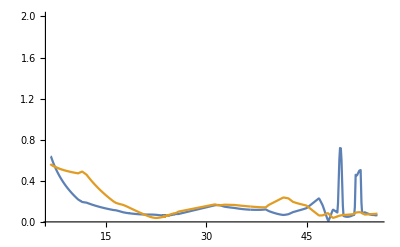

```mathematica
ListLinePlot[{Join[Transpose[{z,xrms}],Transpose[{s+Last[z],10^3 Sx}]],Join[Transpose[{z,yrms}],Transpose[{s+Last[z],10^3 Sy}]]},PlotRange->{All,{0,2}}]
```

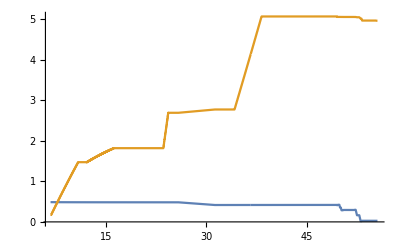

```mathematica
ListLinePlot[{Join[Transpose[{z,zrms}],Transpose[{s+Last[z],10^3 2.99 10^8 St}]],Join[Transpose[{z,10^-3 ΔErms}],Transpose[{s+Last[z],Ekin[[-1]] Sdelta}]]},PlotRange->All]
```

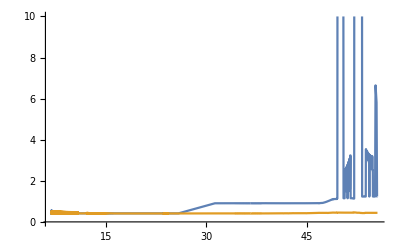

```mathematica
ListLinePlot[{Join[Transpose[{z,ϵxnorm}],Transpose[{s+Last[z],10^6 enx}]],Join[Transpose[{z,ϵynorm}],Transpose[{s+Last[z],10^6 eny}]]},PlotRange->{All,{0,10}}]
```

```mathematica
{x,y,z,cpx,cpy,cpz,t,q}=Transpose[Import["./CLA-FEB-W-FOCUS.hdf5","/beam/beam"]];
```

Import::nffil: File not found during Import.

Set::shape: Lists {x,y,z,cpx,cpy,cpz,t,q} and Transpose[$Failed] are not the same shape.

```mathematica
lplot=ListPlot[{10^6 Transpose[{x,y}][[1;;-1;;10]]},AspectRatio->Automatic,Frame->True,ImageSize->600,PlotStyle->{{Red}},PlotRange->All]
```

Transpose::nmtx: The first two levels of {x,y} cannot be transposed.

-Graphics-

```mathematica
lplot=ListPlot[{Transpose[{10^12(z-Mean[z])/(2.98 10^8),10^-6 cpz}][[1;;-1;;10]]},AspectRatio->1,Frame->True,ImageSize->600,PlotStyle->{{Red,Opacity[0.1]}}]
```

Transpose::nmtx: The first two levels of {{-58014.8,-58002.7,-57989.3,-57976.2,-57962.8,-57949.4,-57936.,-57923.2,-57909.8,-57896.4,-57883.3,-57869.9,-57856.4,«26»,-57498.7,-57485.3,-57471.9,-57458.4,-57446.,-57432.6,-57419.2,-57405.8,-57392.3,-57379.6,-57366.2,«9435»},cpz/(1«4»00)} cannot be transposed.

Transpose::nmtx: The first two levels of {{-58014.8,-58002.7,-57989.3,-57976.2,-57962.8,-57949.4,-57936.,-57923.2,-57909.8,-57896.4,-57883.3,-57869.9,-57856.4,«26»,-57498.7,-57485.3,-57471.9,-57458.4,-57446.,-57432.6,-57419.2,-57405.8,-57392.3,-57379.6,-57366.2,«9435»},1.×10^-6 cpz} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

-Graphics-

```mathematica
slicelength=0.0005;
ListLinePlot[{#[[1]],Append[#[[2]],0]}//Transpose,Frame->True,PlotRange->{All,All},FrameLabel->{"t [ps]","I [A]"}]&[{1,250/(slicelength Length[#])}HistogramList[#,{slicelength}]]&[10^12(z-Mean[z])/(2.99 10^8)]
```

$Aborted

## Plotting Emit Files

```mathematica
<<astrainterpret`
```

```mathematica
<<sddsBinaryinterpret`
```

```mathematica
SetDirectory["\\\\apclara1\\jkj62\\OnlineModel\\SimulationFramework\\Examples\\CLARA\\test"]
```

\\apclara1\jkj62\OnlineModel\SimulationFramework\Examples\CLARA\test

```mathematica
ASTRAemitInterpret["./"~~#~~".Zemit.001"&/@{"L02","S03","L03","S04","L4H","S05","S06","L04","S07","FMS"},ASTRAVerbose->True]
```

Columns Redefined: z [m], t [ns], xavr [mm], xrms [mm], xprms [mrad], ϵxnorm [mm mrad π], xxpavr [mm mrad]

Columns Redefined: z [m], t [ns], yavr [mm], yrms [mm], yprms [mrad], ϵynorm [mm mrad π], yypavr [mm mrad]

Columns Redefined: z [m], t [ns], Ekin [MeV], zrms [mm], ΔErms [keV], ϵznorm [keV mm π], zEavr [keV]

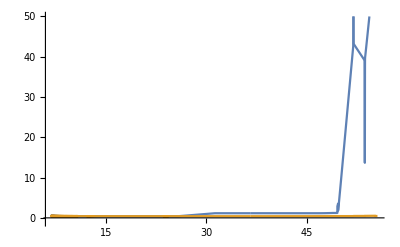

```mathematica
ListLinePlot[{Join[Transpose[{z,ϵxnorm}]],Join[Transpose[{z,ϵynorm}]]},PlotRange->{All,{-1,50}}]
```

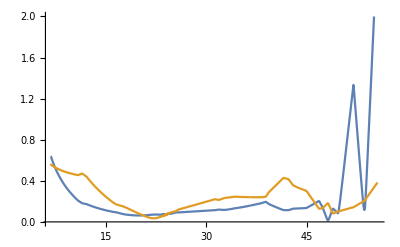

```mathematica
ListLinePlot[{Join[Transpose[{z,xrms}]],Join[Transpose[{z,yrms}]]},PlotRange->{All,{0,2}}]
```

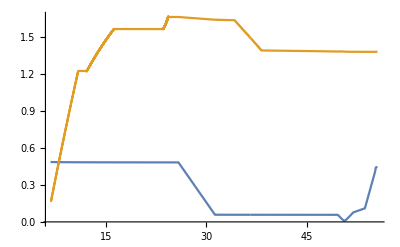

```mathematica
ListLinePlot[{Join[Transpose[{z,zrms}]],Join[Transpose[{z,10^-3 ΔErms}]]},PlotRange->All]
```

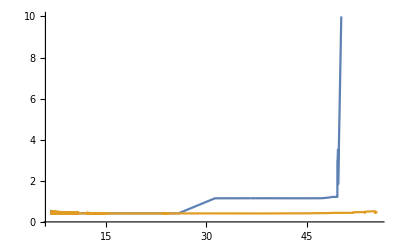

```mathematica
ListLinePlot[{Join[Transpose[{z,ϵxnorm}]],Join[Transpose[{z,ϵynorm}]]},PlotRange->{All,{0,10}}]
```

```mathematica
{x,y,z,cpx,cpy,cpz,t,q}=Transpose[Import["./CLA-FEB-W-FOCUS.hdf5","/beam/beam"]];
```

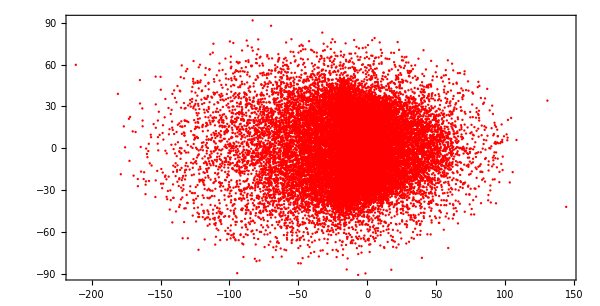

```mathematica
lplot=ListPlot[{10^6 Transpose[{x,y}][[1;;-1;;10]]},AspectRatio->Automatic,Frame->True,ImageSize->600,PlotStyle->{{Red}},PlotRange->All]
```

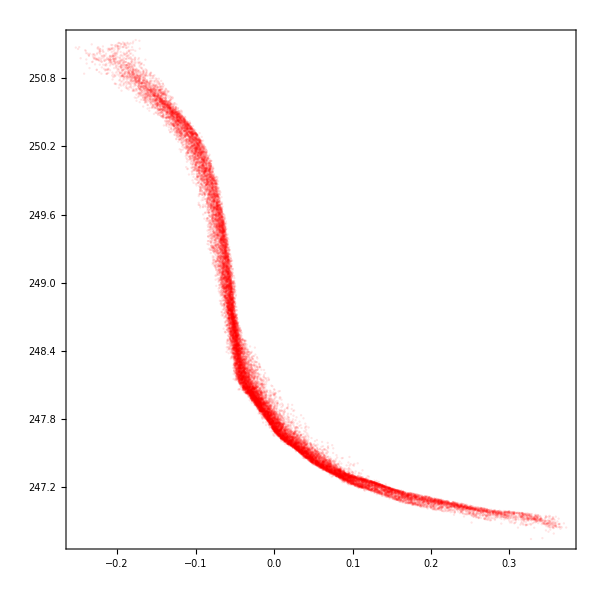

```mathematica
lplot=ListPlot[{Transpose[{10^12(z-Mean[z])/(2.98 10^8),10^-6 cpz}][[1;;-1;;10]]},AspectRatio->1,Frame->True,ImageSize->600,PlotStyle->{{Red,Opacity[0.1]}}]
```

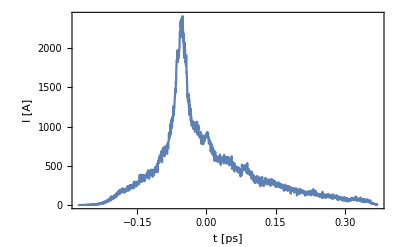

```mathematica
slicelength=0.0005;
ListLinePlot[{#[[1]],Append[#[[2]],0]}//Transpose,Frame->True,PlotRange->{All,All},FrameLabel->{"t [ps]","I [A]"}]&[{1,250/(slicelength Length[#])}HistogramList[#,{slicelength}]]&[10^12(z-Mean[z])/(2.99 10^8)]
```